### Simulate the MRI 3 axis device

```mathematica
maxAngle = 30/180 π; (*page 93, the capture volume is π/9, or 1/12 the volume of a sphere.*)
DrawRotor[trans_,rotAng_,rotVec_,spinAngle_]:=Rotate[Translate[Rotate[Module[{rollerRad = 5,
rotorRad = 20,
sphereRad = 6,
rotorThick = 1,
bracketThick = 2
},{
{White,
Opacity[0.5],
Cuboid[{
{sphereRad-rotorThick,-rotorRad-sphereRad,-rotorThick-sphereRad+rotorThick},{+sphereRad+rotorThick,rotorRad+sphereRad,rotorThick+sphereRad-rotorThick}}],
Cuboid[{
{-sphereRad-rotorThick,-rotorRad-sphereRad,-rotorThick-sphereRad+rotorThick},{-sphereRad+rotorThick,rotorRad+sphereRad,rotorThick+sphereRad-rotorThick}}]},
Black,
Cylinder[{{-3bracketThick-sphereRad,0,0},{+sphereRad+3rotorThick,0,0}},1 ],
(*ferrous sphere*)
Gray,
Sphere[{0,-rotorRad,0},sphereRad]
}],spinAngle,{1,0,0}],trans],-rotAng,rotVec];
vp=Options[Graphics3D,ViewPoint][[1,2]];
drawNeedleActuator[θx_,θy_,Horiz_,ShowScan_,ShowLevel_,OpacityVal_,gearbox3Length_,gearboxLength_,needleDepth_,viewPt_,imgSize_]:=Module[{
(*units in mm*)
hoopRad = 50,
gearRatio =10,
hoopWid = 3/2,
carriageWidthHalf =3,
baseHingeHeight = 8,
CarriageThicknessHalf = 2,
bracketThick = 2,
MinSeparation = 1000*0.11641453227603929/2 + 20 (*add in the radius of the rotor*),
xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2),
x=Cos[θx] Sin[θy],
y=-Cos[θy] Sin[θx],
z=Cos[θx] Cos[θy],
scanRot,
tipAng,
rollerRad = 5,
rotorRad = 20,
sphereRad = 6,
rotorThick = 1
},

Graphics3D[{

{(*base*)
White,{Opacity[0.6],
Cylinder[{{0,0,-baseHingeHeight-bracketThick},{0,0,-baseHingeHeight}},hoopRad]},

Module[(*brackets*)
{
bwid =carriageWidthHalf+bracketThick, 
bbottom=-baseHingeHeight-bracketThick,
btop=baseHingeHeight},
{Cuboid[{{+hoopRad+bracketThick,-bwid,bbottom},{+hoopRad,bwid,btop}}],
Cuboid[{{-hoopRad-bracketThick,-bwid,bbottom},{-hoopRad,bwid,btop}}],
Cuboid[{{-bwid,+hoopRad+bracketThick,bbottom},{bwid,+hoopRad,btop}}],
Cuboid[{{-bwid,-hoopRad-bracketThick,bbottom},{bwid,-hoopRad,btop}}]
}
]
},

If[ShowScan,
(*Scan plane*)
{Gray,
tipAng = π;
scanRot = RotationMatrix[tipAng,{1,1,1}];
 Arrow[120{{0,0,0},scanRot.{1,0,0}}],
 Arrow[120{{0,0,0},scanRot.{0,1,0}}],
Opacity[0.5],
Polygon[120Table[scanRot.v,{v,{{1,1,0},{1,-1/2,0},{-1/2,-1/2,0},{-1/2,1,0}}}]]
(*Polygon[100{{√2,-√2,0},{√2,√2,2},{-√2,√2,0},{-√2,-√2,-2}}]*)
}],

(*hoop1*)
Blue, Thick,
If[OpacityVal>0,{Opacity[OpacityVal],Sphere[{0,hoopRad+gearboxLength,baseHingeHeight},MinSeparation]}],
(*gearbox*)
Cylinder[{{0,hoopRad+bracketThick,0},{0,hoopRad+gearboxLength-sphereRad-2rotorThick,0}},baseHingeHeight],
(*axels*)
Cylinder[{{0,hoopRad-2bracketThick,0},{0,hoopRad,0}},2carriageWidthHalf ],
Cylinder[{{0,-hoopRad+2bracketThick,0},{0,-hoopRad,0}},2carriageWidthHalf ],
Rotate[{
(*Cylinder[{{-carriageWidthHalf,0,0},{carriageWidthHalf,0,0}},hoopRad],*)
Tube[BSplineCurve[Table[{-carriageWidthHalf, hoopRad Cos[θ], hoopRad Sin[θ]},{θ,0,π,π/6}]],hoopWid],
Tube[BSplineCurve[Table[{carriageWidthHalf, hoopRad Cos[θ], hoopRad Sin[θ]},{θ,0,π,π/6}]],hoopWid]},
θy,{0,1,0}],
DrawRotor[{hoopRad+gearboxLength,0,0},-π/2,{0,0,1},gearRatio θy],


(*hoop2*)
Red, Thick,
If[OpacityVal>0,{Opacity[OpacityVal],Sphere[{hoopRad+gearboxLength,0,baseHingeHeight},MinSeparation]}],
(*gearbox*)
Cylinder[{{hoopRad+bracketThick,0,0},{hoopRad+gearboxLength-sphereRad-2rotorThick,0,0}},baseHingeHeight],
(*axels*)
Cylinder[{{hoopRad-4bracketThick,0,0},{hoopRad,0,0}},2carriageWidthHalf ],
Cylinder[{{-hoopRad+4bracketThick,0,0},{-hoopRad,0,0}},2carriageWidthHalf ],
Rotate[{
(*hoops*)
(*Cylinder[{{0,-carriageWidthHalf,0},{0,carriageWidthHalf,0}},hoopRad],*)
Tube[BSplineCurve[Table[{ (hoopRad-2hoopWid) Cos[θ],-carriageWidthHalf, (hoopRad-2hoopWid) Sin[θ]},{θ,0,π,π/6}]],hoopWid],
Tube[BSplineCurve[Table[{ (hoopRad-2hoopWid) Cos[θ],carriageWidthHalf,  (hoopRad-2hoopWid) Sin[θ]},{θ,0,π,π/6}]],hoopWid]},θx,{1,0,0}],
DrawRotor[{hoopRad+gearboxLength,0,0},0,{0,0,1},gearRatio θx],

(*carriage:  *)
Green,
(*Text[StringForm["``",ArcTan[z,x]],{0,0,0}],*)
Rotate[Rotate[{
(*PointSize[.05],Green,Point[{0,0,hoopRad}],*)

Cuboid[{-carriageWidthHalf,-carriageWidthHalf,hoopRad-CarriageThicknessHalf},{carriageWidthHalf,carriageWidthHalf,hoopRad+CarriageThicknessHalf}],

If[Horiz,{
(*gearbox, horizontal, 102 min length*)
Cylinder[{{(-2carriageWidthHalf)/(√2),(-2carriageWidthHalf)/(√2),baseHingeHeight+hoopRad},{(-gearbox3Length+sphereRad+2rotorThick)/(√2),(-gearbox3Length+sphereRad+2rotorThick)/(√2),baseHingeHeight+hoopRad}},baseHingeHeight],
(*Rollers*)
Cylinder[{{(rollerRad-2carriageWidthHalf)/(√2),(-rollerRad-2carriageWidthHalf)/(√2),baseHingeHeight+hoopRad},{(2carriageWidthHalf+rollerRad)/(√2),(2carriageWidthHalf-rollerRad)/(√2),baseHingeHeight+hoopRad}},rollerRad],
Cylinder[{{(-rollerRad-2carriageWidthHalf)/(√2),(rollerRad-2carriageWidthHalf)/(√2),baseHingeHeight+hoopRad},{(2carriageWidthHalf-rollerRad)/(√2),(2carriageWidthHalf+rollerRad)/(√2),baseHingeHeight+hoopRad}},rollerRad],


{Opacity[OpacityVal],Sphere[{-1/√2gearbox3Length,-1/√2gearbox3Length,baseHingeHeight+hoopRad},MinSeparation]},
DrawRotor[{gearbox3Length,0,baseHingeHeight+hoopRad},3/4π,{0,0,1},needleDepth]

}
,{
(*gearbox, vertical, 147 min length*)
Cylinder[{{-1/√2baseHingeHeight,-1/√2baseHingeHeight,hoopRad},{-1/√2baseHingeHeight,-1/√2baseHingeHeight,gearbox3Length+hoopRad-sphereRad-2rotorThick}},baseHingeHeight],
(*Rollers*)
Cylinder[{{(rollerRad-2carriageWidthHalf)/(√2),(-rollerRad-2carriageWidthHalf)/(√2),-baseHingeHeight-rollerRad+hoopRad},{(2carriageWidthHalf+rollerRad)/(√2),(2carriageWidthHalf-rollerRad)/(√2),-baseHingeHeight-rollerRad+hoopRad}},rollerRad],
Cylinder[{{(-rollerRad-2carriageWidthHalf)/(√2),(rollerRad-2carriageWidthHalf)/(√2),-baseHingeHeight-rollerRad+hoopRad},{(2carriageWidthHalf-rollerRad)/(√2),(2carriageWidthHalf+rollerRad)/(√2),-baseHingeHeight-rollerRad+hoopRad}},rollerRad],

DrawRotor[{-1/√2baseHingeHeight,-1/√2baseHingeHeight,gearbox3Length+hoopRad},0π,{1,0,0},needleDepth],
If[OpacityVal>0,
{Opacity[OpacityVal],Sphere[{-1/√2baseHingeHeight,-1/√2baseHingeHeight,gearbox3Length+hoopRad},MinSeparation]}]
}]
},
ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}],
ArcTan[z,x],{0,1,0}],
(*needle*)Black,
Tube[{(2-needleDepth/100)2hoopRad/xyzNorm{x,y,z},{0,0,0},If[ShowLevel,-needleDepth/100 ,-0.15]* 2hoopRad/xyzNorm{x,y,z}},1],
(*draw range of needle*)
If[ShowLevel,solidNeedleRange]
(*,Opacity[0],Sphere[{0,0,0},120]*)
},ImageSize->imgSize,Boxed->False,(*SphericalRegion->True,*)
(*ViewCenter->{{1/2,1/2,1/2},{1/2,1/2}},*)
ViewPoint->viewPt(* Dynamic[vp]*)
]];
Manipulate[
drawNeedleActuator[θx,θy,Horiz,ShowScan,ShowLevel,OpacityVal,gearbox3Length,gearboxLength,needleDepth,Dynamic[vp],200]
,
{{θx,-maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{θy,maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{Horiz,True},{True,False}},
{{ShowScan,False},{True,False}},
{{ShowLevel,False},{True,False}},
{{OpacityVal,0},0,1},
{{gearbox3Length,75},0,150,Appearance->"Labeled"},
{{gearboxLength,75},0,150,Appearance->"Labeled"},
{{needleDepth,100},0,100,Appearance->"Labeled"}
]
Dynamic[vp]
```

```mathematica
Settings for lead photo:
ViewPoint->{1.1596889537706192,-3.027633036377363,0.9687929229400873}(*Dynamic[vp]*)
]],
{{θx,-maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{θy,-maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{Horiz,True},{True,False}},
{{ShowScan,False},{True,False}},
{{ShowLevel,True},{True,False}},
{{OpacityVal,0.0},0,1},
{{gearbox3Length,75},0,150,Appearance->"Labeled"},
{{gearboxLength,75},0,150,Appearance->"Labeled"},
{{needleDepth,100},0,100,Appearance->"Labeled"}


Settings for scan plane photo:
ViewPoint->{-2.28163,-2.17383,1.23233}(* Dynamic[vp]*)
]],
{{θx,maxAngle/2},-maxAngle,maxAngle,Appearance->"Labeled"},
{{θy,maxAngle/2},-maxAngle,maxAngle,Appearance->"Labeled"},
{{Horiz,True},{True,False}},
{{ShowScan,True},{True,False}},
{{ShowLevel,False},{True,False}},
{{OpacityVal,0.0},0,1},
{{gearbox3Length,75},0,150,Appearance->"Labeled"},
{{gearboxLength,75},0,150,Appearance->"Labeled"},
{{needleDepth,100},0,100,Appearance->"Labeled"}

for candidate designs photo:
]],
{{θx,-maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{θy,maxAngle},-maxAngle,maxAngle,Appearance->"Labeled"},
{{Horiz,True},{True,False}},
{{ShowScan,False},{True,False}},
{{ShowLevel,False},{True,False}},
{{OpacityVal,0.28},0,1},
{{gearbox3Length,75},0,150,Appearance->"Labeled"},
{{gearboxLength,75},0,150,Appearance->"Labeled"},
{{needleDepth,100},0,100,Appearance->"Labeled"}
]
```

```mathematica
drawNeedleActuator[θ,0,True,False,True,0,75,75,0,{1,-2.4,2},200]
```

-Graphics3D-

### Make a movie

```mathematica
(*drawNeedleActuator[θx,θy,Horiz,ShowScan,ShowLevel,OpacityVal,gearbox3Length,gearboxLength,needleDepth,{-2.28163,-2.17383,1.23233},200]*)
```

```mathematica
Table[drawNeedleActuator[θ,0,True,False,True,0,75,75,0,{1,-2.4,2},200],{θ,0,2}],
Table[drawNeedleActuator[0,0,True,False,True,0,75,75,d,{1,-2.4,2},200],{d,0,100,20}],
Table[drawNeedleActuator[θ,0,True,False,True,0,75,75,0,{1,-2.4,2},200],{θ,2,0,-1}]
```

```mathematica
SessionTime[]
px = {2000,1600};
vp = {1,-2.4,2};
frames =Flatten[{
Table[drawNeedleActuator[θ,-θ,True,False,True,0,75,75,0,vp,px],{θ,0,π/6,π/(6*90)}],
Table[drawNeedleActuator[π/6,-π/6,True,False,True,0,75,75,d,vp,px],{d,0,100,100/90}],
Table[drawNeedleActuator[π/6,-π/6,True,False,True,0,75,75,d,vp,px],{d,100,0,-100/90}],
Table[drawNeedleActuator[θ,-θ,True,False,True,0,75,75,0,vp,px],{θ,π/6,0,-π/(6*90)}]}
];
SessionTime[]
```

29029.55967

29030.32343

```mathematica
Length[frames]
```

364

```mathematica
SessionTime[]
Export["needleTiltFull2.mov",frames]
SessionTime[]
```

29092.46292

needleTiltFull2.mov

29865.51455

```mathematica
Directory[]
```

/Users/ab55

```mathematica
SessionTime[]
Export["needleTiltFull.mpeg",frames]
SessionTime[]
```

28805.23674

Export::infer: Cannot infer format of file "needleTiltFull.mpeg".

$Failed

28805.25356

### Minimium separation between components in Walsh MRI design

```mathematica
-(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4) (*Dipole-dipole maximum force for distance y*)
4/3 π r1^3 Msat grad  (*assume r1 ≤ r2, so this is the minimum force... only depends on larger one anyway*)
```

```mathematica
Solve[(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4)==percentage/100 4/3 π r1^3 Msat grad,{y}]
```

{{y→-(2^(3/4) √5 Msat^(1/4) r2^(3/4) μ0^(1/4))/(grad^(1/4) percentage^(1/4))},{y→-(ⅈ 2^(3/4) √5 Msat^(1/4) r2^(3/4) μ0^(1/4))/(grad^(1/4) percentage^(1/4))},{y→(ⅈ 2^(3/4) √5 Msat^(1/4) r2^(3/4) μ0^(1/4))/(grad^(1/4) percentage^(1/4))},{y→(2^(3/4) √5 Msat^(1/4) r2^(3/4) μ0^(1/4))/(grad^(1/4) percentage^(1/4))}}

```mathematica
Solve[(8 Msat^2 π r1^3 r2^3 μ0)/(3 y^4)==percentage/100 4/3 π r1^3 Msat grad /.{μ0-> 4π 10^-7,
Msat->1.36 10^6,r1->.005,r2->.006,percentage->10,grad->0.04},{y},Reals]
```

{{y→-0.116558},{y→0.116558}}

```mathematica
5.40*(.006)^(3/4)
```

0.116415

```mathematica
μ0=4π 10^-7;
Msat=  1.36 10^6;
Solve[((2 100/percentage Msat r1^3 μ0)/0.04)^(1/4)==√(2)(0.050+d-0.018)/.{percentage->10,r1->.006},{d}]
```

{{d→0.0504192}}

```mathematica
((2 100/percentage Msat r1^3 μ0)/0.04)^(1/4)/.{percentage->10,r1->.003,μ0-> 4π 10^-7,
Msat->  1.36 10^6}
```

0.069306

```mathematica
Force = r^3*d,
```

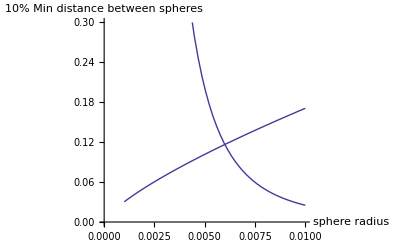

```mathematica
Plot[{((2 100/percentage Msat r1^3 μ0)/0.04)^(1/4),0.11655828049811334(0.006/r1)^3}/.{percentage->10,μ0-> 4π 10^-7,
Msat->  1.36 10^6},{r1,0.001,0.01},AxesOrigin->{0,0},PlotRange->{{0,0.01},{0,0.3}},AxesLabel->{"sphere radius","10% Min distance between spheres"}]
```

```mathematica
(*this matches Walsh's work on page 113.  I think it is wrong*)
RotationMatrix[θy,{0,1,0}].RotationMatrix[θx,{1,0,0}]//MatrixForm
```

(Cos[θy] | Sin[θx] Sin[θy] | Cos[θx] Sin[θy]
0 | Cos[θx] | -Sin[θx]
-Sin[θy] | Cos[θy] Sin[θx] | Cos[θx] Cos[θy])

```mathematica
Manipulate[Module[{xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2),
x=-Cos[θx] Sin[θy],
y=Cos[θy] Sin[θx],
z=Cos[θx] Cos[θy]},

Show[Graphics3D[{PointSize->Large,
Blue,
Point[{x,y,z}/xyzNorm],
Red,(*Walsh's method*)
Point[{0,0,1}.RotationMatrix[θy,{0,1,0}].RotationMatrix[θx,{1,0,0}]],
Green,

Point[{0,0,1}.RotationMatrix[-ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}].RotationMatrix[-ArcTan[z,x],{0,1,0}]]

}],

ParametricPlot3D[{
{Cos[θ],Sin[θ] Sin[θx],Cos[θx] Sin[θ]} ,

 {-Sin[θ] Sin[θy],Cos[θ],Cos[θy] Sin[θ]}
},
{θ,0,π} (*,PlotStyle->Thick*)

]]],{{θx,0},-π/2,π/2},{{θy,0},-π/2,π/2}]
```

### Intersection of two planes to find the true intersection point in our cradle.

```mathematica
Clear[θx,θy]
n1 = {Cos[θy],0,Sin[θy]};
n2 = {0,Cos[θx],Sin[θx]};
n1×n2
vecNorm[vec_?VectorQ]:=Sqrt[vec.vec]
FullSimplify[Normalize[n1×n2,vecNorm],Reals]
```

{-Cos[θx] Sin[θy],-Cos[θy] Sin[θx],Cos[θx] Cos[θy]}

{-(Cos[θx] Sin[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),(Cos[θx] Cos[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))}

```mathematica
Plot3D[Cos[θx] Cos[θy],{θx,-π/2,π/2},{θy,-π/2,π/2}]
```

-Graphics3D-

### Find Lat/Long Coordinates corresponding to the inputs

```mathematica
{(Cos[θx] Sin[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),(Cos[θx] Cos[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))}
```

```mathematica
x=Cos[θx] Sin[θy];
y=-Cos[θy] Sin[θx];
z=Cos[θx] Cos[θy];

FullSimplify[ArcTan[√(1-(y/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)))^2),-y/√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)]]
FullSimplify[ArcTan[z,x]]
```

ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]

ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]

```mathematica
FullSimplify[RotationMatrix[ArcTan[√(1-(y/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)))^2),-y/√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)],{1,0,0}].RotationMatrix[ArcTan[z,x],{0,1,0}]]//MatrixForm
```

(Cos[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]] | 0 | Sin[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]]
Sin[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]] Sin[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]] | Cos[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]] | -Cos[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]] Sin[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]]
-Cos[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]] Sin[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]] | Sin[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]] | Cos[ArcTan[Cos[θx] Cos[θy],Cos[θx] Sin[θy]]] Cos[ArcTan[√(1/(1+Cos[θy]^2 Tan[θx]^2)),(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))]])

```mathematica
Clear[θx,θy,x,y,z]
Solve[x^2+y^2+z^2==1 && z Tan[θx] == y &&z Tan[θy] == x,{x,y,z}]
```

{{x→-Tan[θy]/(√(1+Tan[θx]^2+Tan[θy]^2)),y→-Tan[θx]/(√(1+Tan[θx]^2+Tan[θy]^2)),z→-1/(√(1+Tan[θx]^2+Tan[θy]^2))},{x→Tan[θy]/(√(1+Tan[θx]^2+Tan[θy]^2)),y→Tan[θx]/(√(1+Tan[θx]^2+Tan[θy]^2)),z→1/(√(1+Tan[θx]^2+Tan[θy]^2))}}

### Plot the Workspace reachable by the needle

```mathematica
pA = π/6;
∫_0^rad ∫_-pA^pA ∫_(π/2-pA)^(π/2+pA) r^2 Sin[θy]ⅆθyⅆθxⅆr
```

(π rad^3)/9

```mathematica
(4 π)/3/(π/9)
```

12

```mathematica
∫_0^1 ∫_0^(2π) ∫_0^π r^2 Sin[θy]ⅆθyⅆθxⅆr
```

(4 π)/3

```mathematica
T={(Cos[θx] Sin[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-(Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),(Cos[θx] Cos[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))};

pA = π/6;
Tdx =FullSimplify[D[T,θx]]
Tdy =FullSimplify[D[T,θy]]
T1 =Tdx/.{θx-> pA,θy->pA}
T2 = Tdy/.{θx-> pA,θy->pA}
IntAng = ArcCos[ T1.T2/(Norm[T1]*Norm[T1])];
N[IntAng]*180/π
SphericalQuadrangle = 4 IntAng - (4-2)π;
N[SphericalQuadrangle]
N[4π]
```

{-(Cos[θy]^2 Sin[θx] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θx] Cos[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θy]^3 Sin[θx])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2))}

{(Cos[θx] Cos[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),(Cos[θx]^2 Sin[θx] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θx]^3 Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2))}

{-4/(5 √15),-16/(5 √15),-4/(5 √5)}

{16/(5 √15),4/(5 √15),-4/(5 √5)}

104.478

1.01072

12.5664

```mathematica
N[Sqrt[2]Sin[π/3]]
```

1.22474

```mathematica
ArcSin[Sqrt[2]Sin[π/3]]
```

```mathematica
N[ArcSin[√(3/2)]]
```

1.5708-0.658479 ⅈ

```mathematica
ArcCos[(Cos[ArcSin[√(3/2)]]-Cos[π/3]Cos[π/3])/(Sin[π/3]Sin[π/3])]
```

ArcCos[4/3 (-1/4+ⅈ/(√2))]

```mathematica
FullSimplify[Norm[({-(Cos[θy]^2 Sin[θx] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θx] Cos[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θy]^3 Sin[θx])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2))})×{(Cos[θx] Cos[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),(Cos[θx]^2 Sin[θx] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2)),-(Cos[θx]^3 Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^(3/2))}]]
```

√(Abs[(Cos[θx]^2 Cos[θy] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^2)]^2+Abs[(Cos[θx] Cos[θy]^2 Sin[θx] (Cos[θy]^2+Cos[θx]^2 Sin[θy]^2))/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^3)]^2+Abs[(Cos[θx]^2 Cos[θy]^2 (1-Sin[θx]^2 Sin[θy]^2))/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^3)]^2)

```mathematica
(∫_(- π/6)^(π/6) (∫_(- π/6)^(π/6) √(Abs[(Cos[θx]^2 Cos[θy] Sin[θy])/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^2)]^2+Abs[(Cos[θx] Cos[θy]^2 Sin[θx] (Cos[θy]^2+Cos[θx]^2 Sin[θy]^2))/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^3)]^2+Abs[(Cos[θx]^2 Cos[θy]^2 (1-Sin[θx]^2 Sin[θy]^2))/((Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)^3)]^2)ⅆθx)ⅆθy)
```

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First :: normal will be suppressed during this calculation.

```mathematica
(*find the angle be
```

```mathematica
Clear[zvIn]
angRange = π/6;
solidNeedleRange =ParametricPlot3D[{zv = zvIn/(2angRange)+1/2; 100zv (Cos[θx] Sin[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-100zv (Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-100zv (Cos[θx] Cos[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))}/.{{θy->angRange,θx->p1,zvIn-> p2},
{θy->-angRange,θx->p1,zvIn-> p2},
{θy->p1,θx->angRange,zvIn-> p2},
{θy->p1,θx->-angRange,zvIn-> p2},
{θy->p1,θx->p2,zvIn-> angRange}},{p1,-angRange,angRange},
{p2,-angRange,angRange},BoxRatios->Automatic,PlotStyle->Directive[Specularity[White, 40],Yellow,Opacity[0.5]],Mesh->None][[1]];
Graphics3D[solidNeedleRange]
```

-Graphics3D-

```mathematica
FindDivisions[{-.5,1},5]
```

{-1/2,0,1/2,1}

```mathematica
Clear[zvIn]
angRange = π/6;
lvlSets = ParametricPlot3D[Table[{zv = zvIn/(2angRange)+1/2; 100zv (Cos[θx] Sin[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-100zv (Cos[θy] Sin[θx])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2)),-100zv (Cos[θx] Cos[θy])/(√(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2))}/.
{θy->p1,θx->p2},{zvIn,angRange{0,1/4,1/2,3/4,1} }],{p1,-angRange,angRange},
{p2,-angRange,angRange},BoxRatios->Automatic,PlotStyle->Directive[Specularity[White, 40],Gray,Opacity[0.5]],Mesh->None][[1]];
Show[Graphics3D[lvlSets]]
```

-Graphics3D-

### What gear system do I need? What force? For axis my max torque is 100 Nmm (page 93)

```mathematica
MaxGravityTorque[hoopRad_(*in m*),gearboxlength_(*in m*), maxAngle_(*in Rad*),massMotor_(*in Kg*)]:=(*in Nm*)Sin[maxAngle](hoopRad+gearboxlength)massMotor 9.801;

massCarriage = 0.1;(*kg, page 93*)(* mass of bearing is 0.007 Kg*)
MaxGravityTorque[0.050,0.00,π/6,massCarriage]  
MaxGravityTorque[0.050,0.00,π/6,massCarriage] /250
```

0.0245025

0.00009801

```mathematica
10*0.005/250
```

0.0002

```mathematica
ForceMag[0.005,0.04]
```

0.0284838

```mathematica
Msat = 1.36 10^6;(*A/m, from An MRI-powered and controlled actuator technology for tetherless robotic interventions *)
ForceMag[sphereRad_,grad_]:=4/3 π sphereRad^3 Msat grad
massCapsule[rad_]:=4/3 π rad^3 DensityFerrous;
DensityFerrous = 7850;(*kg/m^3*)
TorqueMotor[sphereRad_,grad_,rotorLen_]:=rotorLen ForceMag[sphereRad,grad]

outputTorqueDesign[efficiency_,sphereRad_,GearRatio_,MaxGrad_,RotorRad_]:=
TorqueMotor[sphereRad,MaxGrad,RotorRad]GearRatio * efficiency 
outputForceDesign[efficiency_,pinionRad_,sphereRad_,GearRatio_,MaxGrad_,RotorRad_]:=
TorqueMotor[sphereRad,MaxGrad,RotorRad]GearRatio * efficiency /pinionRad
TorqueOrientation[depthM_]:=depthM 60/100
```

### Pierre wants 20 N

```mathematica
(*outputForceDesign[efficiency_,pinionRad_,sphereRad_,GearRatio_,MaxGrad_,RotorRad_]*)
outputForceDesign[1,0.005, 0.005,125, 0.023, 0.0325]
Solve[9.4 == outputForceDesign[efficiency,0.005, 0.005,125, 0.023, 0.0325]]
```

13.3073

{{efficiency→0.706381}}

```mathematica
40*5
```

200

```mathematica
(* outputForceDesign[efficiency_,pinionRad_,sphereRad_,GearRatio_,MaxGrad_,RotorRad_] 
http://gears.sariel.pl
*)
Design20NForce = outputForceDesign[0.5,0.005, 0.006,3*3*36, 0.023, 0.032]
```

29.343

```mathematica
(* outputForceDesign[efficiency_,pinionRad_,sphereRad_,GearRatio_,MaxGrad_,RotorRad_] 
http://gears.sariel.pl
*)
Design20NForce = outputForceDesign[0.5,0.005, 0.006,5*5*5*5, 0.023, 0.032]
```

56.603

### What is Reasonable friction values? Keep the same torque, change parameter values to match, and add gravity torque and needle depth torque. My torque output is :

```mathematica
TorqueMotor[0.006,0.04,0.02]
N[7*10^-5]
```

0.000984399

0.00007

```mathematica
(*I need 100Nmm of torque for carriage motors.  3 rotors produce 0.81 torque on average per rotor *)
0.81*outputTorqueDesign[0.5,0.006,250,0.04,0.02]
```

0.0996704

```mathematica
(*I need 50Nmm of torque for needle-insertion motor.  3 rotors produce 0.81 torque on average per rotor *)
0.81*outputTorqueDesign[0.5,0.006,125,0.04,0.02]
```

0.0498352

```mathematica
massCapsule[0.006]
```

0.00710251

```mathematica
(*IJRR designs*)
Design1Force = outputForceDesign[0.2,0.005, 0.003, 125, 0.04, 0.018]
(*I think they want to halve the pinion radius*)
Design2Force = outputForceDesign[0.5,0.0025, 0.006, 125, 0.04, 0.018]
```

0.553725

22.149

### Find a Scan plane

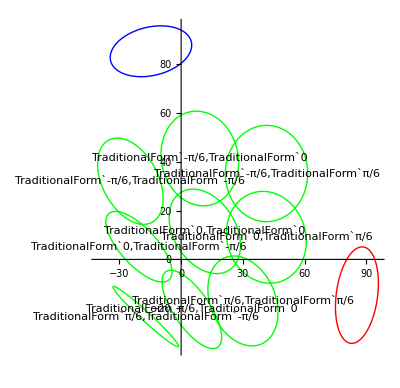

```mathematica
CircleEq[C3_,lat_,long_,rad_,θ_]:=Module[{n,u,v},
n = {Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u ={-Sin[long],Cos[long],0};
v = {Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
C3+rad Cos[θ]u+rad Sin[θ] v]
hoopRad = 50;
gearboxLength =75;
baseHingeHeight = 8;
rotorLength = 20;
gearbox3Length = 60;
markerOffset =-25;
markerOffset3 =-25;
tipAng =1/4 π;


pV1 =RotationMatrix[tipAng,{1,-1,0}].{1,0,0};
pV2 =RotationMatrix[tipAng,{1,-1,0}].{0,1,0};

(*pV1 =Normalize[{0,1,1}];
pV2 = Normalize[  {1,0,1}];*)

Cm1 = {0,hoopRad+gearboxLength+markerOffset,0};
long1 =π/2;
lat1 =π/2;
Cm2 = {hoopRad+gearboxLength+markerOffset,0,0};
long2 =-π;
lat2 =π/2;

Cm3 = {-1/√2(gearbox3Length+markerOffset3),-1/√2(gearbox3Length+markerOffset3),baseHingeHeight+hoopRad};
CircleEq3[C3_,lat_,long_,rad_,θ_,θx_,θy_]:=Module[{n,u,v,RotM,C3rot,xyzNorm,x,y,z},
x=Cos[θx] Sin[θy];
y=-Cos[θy] Sin[θx];
z=Cos[θx] Cos[θy];
xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2);
RotM = RotationMatrix[ArcTan[z,x],{0,1,0}].RotationMatrix[ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}];
n =RotM.{Cos[long] Sin[lat],Sin[long] Sin[lat],Cos[lat]}; (*normal to circle*)
u =RotM.{-Sin[long],Cos[long],0};
v = RotM.{Cos[long] Cos[lat],Cos[lat] Sin[long],-Sin[lat]}; (*v =  n×u *)
C3rot = RotM.C3;
C3rot+rad Cos[θ]u+rad Sin[θ] v]
CenterCircleEq3[C3_,lat_,long_,rad_,θ_,θx_,θy_]:=Module[{RotM,xyzNorm,x,y,z},
x=Cos[θx] Sin[θy];
y=-Cos[θy] Sin[θx];
z=Cos[θx] Cos[θy];
xyzNorm = √(Cos[θx]^2+Cos[θy]^2 Sin[θx]^2);
RotM = RotationMatrix[ArcTan[z,x],{0,1,0}].RotationMatrix[ArcTan[√(1-(y/xyzNorm)^2),-y/xyzNorm],{1,0,0}];
 RotM.C3]
long3 =-3π/4;
lat3 =π/2;

ParametricPlot[
Evaluate[
Ceq1 = CircleEq[Cm1,lat1,long1,rotorLength,θ];
Ceq2 = CircleEq[Cm2,lat2,long2,rotorLength,θ];
{{Ceq1.pV1,Ceq1.pV2},
{Ceq2.pV1,Ceq2.pV2},
Table[Ceq3 = CircleEq3[Cm3,lat3,long3,rotorLength,θ,θxV,θyV];
{Ceq3.pV1,Ceq3.pV2},{θxV,{-π/6,0,π/6}},{θyV,{-π/6,0,π/6}}]}],
{θ,0,2π},AspectRatio->Automatic, PlotStyle->{Blue,Red,Green},
Epilog->{Table[
Ceq3 = CenterCircleEq3[Cm3,lat3,long3,rotorLength,θ,θxV,θyV];
Text[StringForm["``,``",θxV,θyV],{Ceq3.pV1,Ceq3.pV2}],{θxV,{-π/6,0,π/6}},{θyV,{-π/6,0,π/6}}]}
]
```

```mathematica
rollerRad/√2
```

rollerRad/(√2)